This notebook is to verify that there indeed no solutions for some cases.

## Setting Defaults

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
pltcolors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Discrete Beams

```mathematica
spectDBWC1={{1,-0.6},{1,0.1},{1,0.6}}
spectDBWC2={{0.5,-0.6},{1,0.1},{1,0.6}}
spectDBWC3={{0.1,-0.6},{1,0.1},{1,0.6}}

spectDBC1={{-1,-0.6},{1,0.1},{1,0.6}}
spectDBC2={{-0.5,-0.6},{1,0.1},{1,0.6}}
spectDBC3={{-0.1,-0.6},{1,0.1},{1,0.6}}

spectDBWC4={{0.5,0.1},{1,0.4},{1,0.6}}
```

{{1,-0.6},{1,0.1},{1,0.6}}

{{0.5,-0.6},{1,0.1},{1,0.6}}

{{0.1,-0.6},{1,0.1},{1,0.6}}

{{-1,-0.6},{1,0.1},{1,0.6}}

{{-0.5,-0.6},{1,0.1},{1,0.6}}

{{-0.1,-0.6},{1,0.1},{1,0.6}}

{{0.5,0.1},{1,0.4},{1,0.6}}

```mathematica
DBAxialSymOmegaNMAAEqnLHSComplex[0.1,0.1,spectDBWC1]
```

-0.675

```mathematica
maaDBLogDPAbs[omega_,spect_,calRange_:{{-1,1},{-1,1}},pltRange_:{Automatic,Automatic,Automatic}]:=Module[{krealRangeM,kimagRangeM},

krealRangeM=calRange[[1]];
kimagRangeM=calRange[[2]];


DensityPlot[
Log@Abs@DBAxialSymOmegaNMAAEqnLHSComplex[omega,kreal+kimag*I,spect],
{kreal,krealRangeM[[1]],krealRangeM[[2]]},
{kimag,kimagRangeM[[1]],kimagRangeM[[2]]},
PlotLegends->Automatic,PlotRange->pltRange,ImageSize->Large,PlotPoints->100,MaxRecursion->7,PlotLabel->"MAA Log(|f(ω="<>ToString@omega<>",k)|) for spectrum "<>ToString[spect],FrameLabel->{"k.real","k.imag"}
]

]
```

```mathematica
mzapDBLogDPAbs[omega_,spect_,calRange_:{{-1,1},{-1,1}},pltRange_:{Automatic,Automatic,Automatic}]:=Module[{krealRangeM,kimagRangeM},

krealRangeM=calRange[[1]];
kimagRangeM=calRange[[2]];


DensityPlot[
Log@Abs@DBAxialSymOmegaNMZApEqnLHSComplex[omega,kreal+kimag*I,spect],
{kreal,krealRangeM[[1]],krealRangeM[[2]]},
{kimag,kimagRangeM[[1]],kimagRangeM[[2]]},
PlotLegends->Automatic,PlotRange->pltRange,ImageSize->Large,PlotPoints->100,MaxRecursion->7,PlotLabel->"MZA+ Log(|f(ω="<>ToString@omega<>",k)|) for spectrum "<>ToString[spect],FrameLabel->{"k.real","k.imag"}
]

]

mzamDBLogDPAbs[omega_,spect_,calRange_:{{-1,1},{-1,1}},pltRange_:{Automatic,Automatic,Automatic}]:=Module[{krealRangeM,kimagRangeM},

krealRangeM=calRange[[1]];
kimagRangeM=calRange[[2]];


DensityPlot[
Log@Abs@DBAxialSymOmegaNMZAmEqnLHSComplex[omega,kreal+kimag*I,spect],
{kreal,krealRangeM[[1]],krealRangeM[[2]]},
{kimag,kimagRangeM[[1]],kimagRangeM[[2]]},
PlotLegends->Automatic,PlotRange->pltRange,ImageSize->Large,PlotPoints->100,MaxRecursion->7,PlotLabel->"MZA- Log(|f(ω="<>ToString@omega<>",k)|) for spectrum "<>ToString[spect],FrameLabel->{"k.real","k.imag"}
]

]
```

```mathematica
maaDBLogDPAbsPlt=maaDBLogDPAbs[1.5,spectDBC1,{{-3,14},{-2,2}},{Automatic,Automatic,{-10,0.6}}]
```

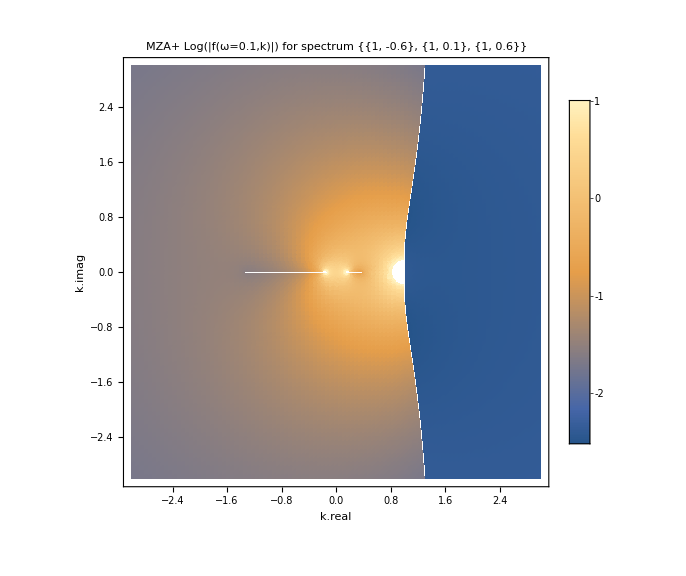
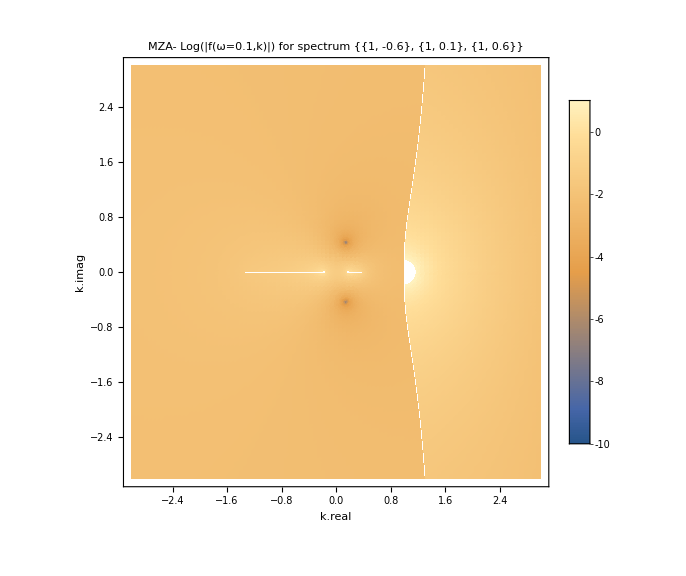
-Graphics- | -Graphics-

```mathematica
mzaDBLogDPAbsPlt=Grid@{{
mzapDBLogDPAbs[0.1,spectDBWC1,{{-3,3},{-3,3}},{Automatic,Automatic,{-10,1}}],
mzamDBLogDPAbs[0.1,spectDBWC1,{{-3,3},{-3,3}},{Automatic,Automatic,{-10,1}}]
}}
```

```mathematica
Export["f-of-omega-0.1-and-k-densityplot-log-mzap-mazm-spectdbwc1.png",
mzaDBLogDPAbsPlt
]
```

f-of-omega-0.1-and-k-densityplot-log-mzap-mazm-spectdbwc1.png

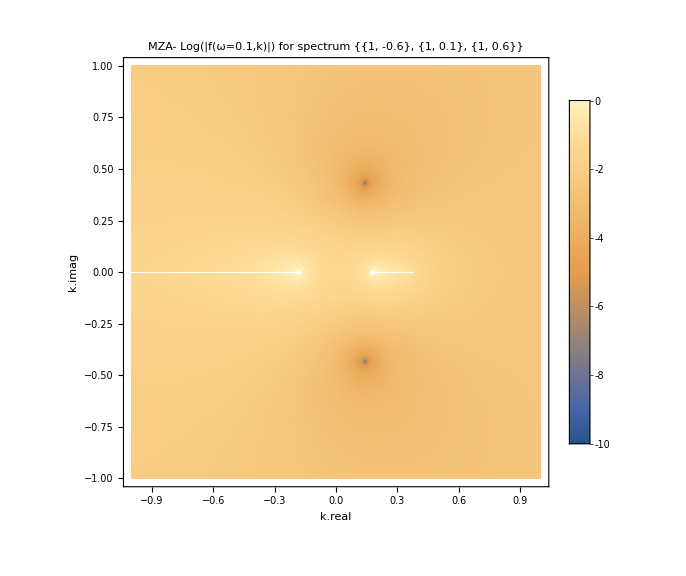

```mathematica
mzamDBLogDPAbs[0.1,spectDBWC1,{{-1,1},{-1,1}},{Automatic,Automatic,{-10,0}}]
```

```mathematica
Log@Abs@DBAxialSymOmegaNMZApEqnLHSComplex[-0.5,-1.99-0*I,spectDBWC1]
```

-5.18447

```mathematica
Export["f-of-omega-0.1-and-k-densityplot-log-mazm-spectdbwc1-2.png",
Out[412]
]
```

f-of-omega-0.1-and-k-densityplot-log-mazm-spectdbwc1-2.png

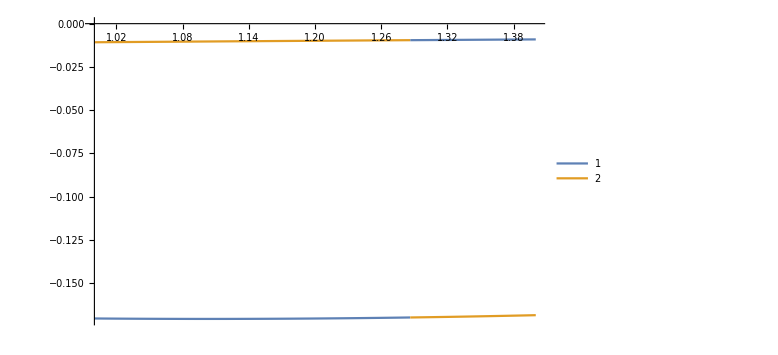

```mathematica
Plot[
{Im@DBAxialSymOmegaNMZApEqnLHSComplex[0.1,kreal-2.75*I,spectDBWC1],
Im@DBAxialSymOmegaNMZAmEqnLHSComplex[0.1,kreal-2.75*I,spectDBWC1]},
{kreal,1,1.4},PlotPoints->100,MaxRecursion->6,PlotLegends->Automatic,ImageSize->Large
]
```

```mathematica
Module[{krealM},

krealM=-1.9;

{Plot[
{Abs@DBAxialSymOmegaNMZApEqnLHSComplex[-0.5,kreal-kimag*I,spectDBWC1],Re@DBAxialSymOmegaNMZApEqnLHSComplex[-0.5,krealM-kimag*I,spectDBWC1],Im@DBAxialSymOmegaNMZApEqnLHSComplex[-0.5,krealM-kimag*I,spectDBWC1]},
{kimag,-0.2,0.2},PlotPoints->100,MaxRecursion->6,PlotLegends->Automatic,ImageSize->Large
],
Plot[
{Re@DBAxialSymOmegaNMZApEqnLHSComplex[-0.5,krealM-kimag*I,spectDBWC1],
Re@DBAxialSymOmegaNMZAmEqnLHSComplex[-0.5,krealM-kimag*I,spectDBWC1]},
{kimag,-0.2,0.2},PlotPoints->100,MaxRecursion->6,PlotLegends->Automatic,ImageSize->Large
]

}

]
```

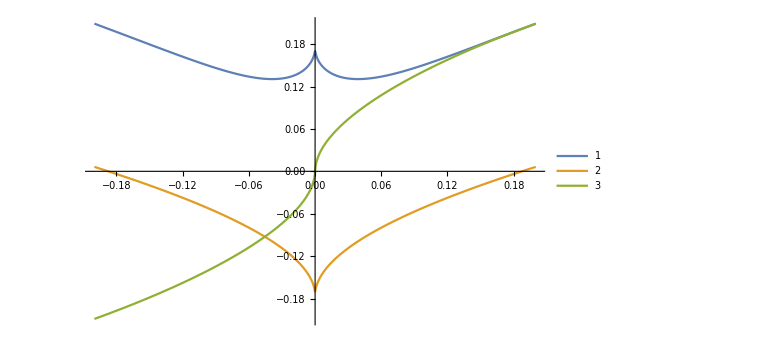
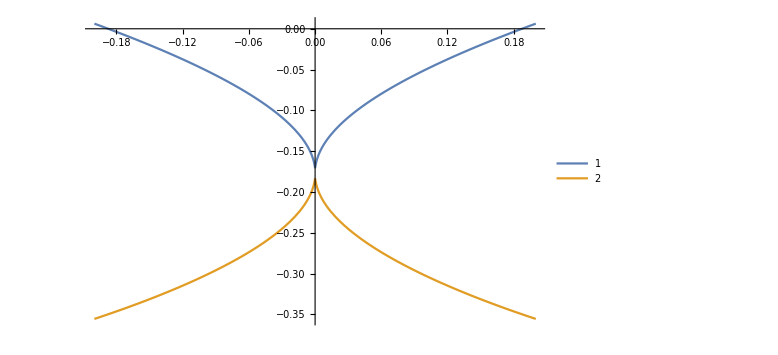

```mathematica
Module[{krealM},

krealM=-1.9;

{Plot[
{Abs@DBAxialSymOmegaNMZApEqnLHSComplex[-0.5,krealM-kimag*I,spectDBWC1],Re@DBAxialSymOmegaNMZApEqnLHSComplex[-0.5,krealM-kimag*I,spectDBWC1],Im@DBAxialSymOmegaNMZApEqnLHSComplex[-0.5,krealM-kimag*I,spectDBWC1]},
{kimag,-0.2,0.2},PlotPoints->100,MaxRecursion->6,PlotLegends->Automatic,ImageSize->Large
],
Plot[
{Re@DBAxialSymOmegaNMZApEqnLHSComplex[-0.5,krealM-kimag*I,spectDBWC1],
Re@DBAxialSymOmegaNMZAmEqnLHSComplex[-0.5,krealM-kimag*I,spectDBWC1]},
{kimag,-0.2,0.2},PlotPoints->100,MaxRecursion->6,PlotLegends->Automatic,ImageSize->Large
]

}

]
```

```mathematica
Re@DBAxialSymOmegaNMZApEqnLHSComplex[-0.5,-1.9-0.01*I,spectDBWC1]
```

-0.137567

## Box Spectrum

define the spectrum

```mathematica
spectWC1={{{-1,-0.3},1},{{-0.3,1},1}};
spectWC2={{{-1,-0.3},0.5},{{-0.3,1},1}};
spectWC3={{{-1,-0.3},0.1},{{-0.3,1},1}};
spectWC4={{{-1,-0.3},0},{{-0.3,1},1}};
```

```mathematica
spectC1={{{-1,-0.3},-0.1},{{-0.3,1},1}};
spectC2={{{-1,-0.3},-0.5},{{-0.3,1},1}};
spectC3={{{-1,-0.3},-1},{{-0.3,1},1}};
spectC4={{{-1,-0.3},-1.5},{{-0.3,1},1}};
```

```mathematica
spectC5={{{-1,-0.3},-15},{{-0.3,1},1}};
spectC6={{{-1,-0.3},-0.01},{{-0.3,1},1}};
spectC7={{{-1,-0.3},0.01},{{-0.3,1},1}};
spectWC5={{{0.1,0.3},1},{{0.3,1},1}};
```

Define Functions

```mathematica
maaLogDPAbs[omega_,spect_,calRange_:{{-1,1},{-1,1}},pltRange_:{Automatic,Automatic,Automatic}]:=Module[{krealRangeM,kimagRangeM},

krealRangeM=calRange[[1]];
kimagRangeM=calRange[[2]];


DensityPlot[
Log@Abs@ConAxialSymOmegaNMAAEqnLHSComplex[omega,kreal+kimag*I,spect],
{kreal,krealRangeM[[1]],krealRangeM[[2]]},
{kimag,kimagRangeM[[1]],kimagRangeM[[2]]},
PlotLegends->Automatic,PlotRange->pltRange,ImageSize->Large,PlotPoints->100,MaxRecursion->7,PlotLabel->"MAA Log(|f(ω="<>ToString@omega<>",k)|) for spectrum "<>ToString[spect],FrameLabel->{"k.real","k.imag"}
]

]
```

```mathematica
mzapLogDPAbs[omega_,spect_,calRange_:{{-1,1},{-1,1}},pltRange_:{Automatic,Automatic,Automatic}]:=Module[{krealRangeM,kimagRangeM},

krealRangeM=calRange[[1]];
kimagRangeM=calRange[[2]];


DensityPlot[
Log@Abs@ConAxialSymOmegaNMZApEqnLHSComplex[omega,kreal+kimag*I,spect],
{kreal,krealRangeM[[1]],krealRangeM[[2]]},
{kimag,kimagRangeM[[1]],kimagRangeM[[2]]},
PlotLegends->Automatic,PlotRange->pltRange,ImageSize->Large,PlotPoints->100,MaxRecursion->7,PlotLabel->"MZA+ Log(|f(ω="<>ToString@omega<>",k)|) for spectrum "<>ToString[spect],FrameLabel->{"k.real","k.imag"}
]

]

mzamLogDPAbs[omega_,spect_,calRange_:{{-1,1},{-1,1}},pltRange_:{Automatic,Automatic,Automatic}]:=Module[{krealRangeM,kimagRangeM},

krealRangeM=calRange[[1]];
kimagRangeM=calRange[[2]];


DensityPlot[
Log@Abs@ConAxialSymOmegaNMZAmEqnLHSComplex[omega,kreal+kimag*I,spect],
{kreal,krealRangeM[[1]],krealRangeM[[2]]},
{kimag,kimagRangeM[[1]],kimagRangeM[[2]]},
PlotLegends->Automatic,PlotRange->pltRange,ImageSize->Large,PlotPoints->100,MaxRecursion->7,PlotLabel->"MZA- Log(|f(ω="<>ToString@omega<>",k)|) for spectrum "<>ToString[spect],FrameLabel->{"k.real","k.imag"}
]

]
```

```mathematica
maaDPARe[omega_,spect_,pltRange_:{Automatic,Automatic,Automatic}]:=Module[{krealRangeM,kimagRangeM},

krealRangeM={-1,1};
kimagRangeM={-1,1};


DensityPlot[
Re@ConAxialSymOmegaNMAAEqnLHSComplex[omega,kreal+kimag*I,spect],
{kreal,krealRangeM[[1]],krealRangeM[[2]]},
{kimag,kimagRangeM[[1]],kimagRangeM[[2]]},
PlotLegends->Automatic,PlotRange->pltRange,ImageSize->Large,PlotPoints->100,MaxRecursion->7
]

]
```

```mathematica
maaDPAIm[omega_,spect_,pltRange_:{Automatic,Automatic,Automatic}]:=Module[{krealRangeM,kimagRangeM},

krealRangeM={-1,1};
kimagRangeM={-1,1};


DensityPlot[
Im@ConAxialSymOmegaNMAAEqnLHSComplex[omega,kreal+kimag*I,spect],
{kreal,krealRangeM[[1]],krealRangeM[[2]]},
{kimag,kimagRangeM[[1]],kimagRangeM[[2]]},
PlotLegends->Automatic,PlotRange->pltRange,ImageSize->Large,PlotPoints->100,MaxRecursion->7
]
]
```

```mathematica
maaP3D[omega_,spect_,calRanges_{{-1,1},{-1,1}},pltRange_:{Automatic,Automatic,{-0.1,0.1}}]:=Module[{krealRangeM,kimagRangeM},

krealRangeM=calRanges[[1]];
kimagRangeM=calRanges[[2]];

{
Plot3D[
{Abs@ConAxialSymOmegaNMAAEqnLHSComplex[omega,kreal+kimag*I,spect],0},
{kreal,krealRangeM[[1]],krealRangeM[[2]]},
{kimag,kimagRangeM[[1]],kimagRangeM[[2]]},
PlotRange->pltRange,ImageSize->Large,AxesLabel->{"kreal","kimag",""},Mesh->All
],
Plot3D[
Re@ConAxialSymOmegaNMAAEqnLHSComplex[omega,kreal+kimag*I,spect],
{kreal,krealRangeM[[1]],krealRangeM[[2]]},
{kimag,kimagRangeM[[1]],kimagRangeM[[2]]},
PlotRange->pltRange,ImageSize->Large
],
Plot3D[
Im@ConAxialSymOmegaNMAAEqnLHSComplex[omega,kreal+kimag*I,spect],
{kreal,krealRangeM[[1]],krealRangeM[[2]]},
{kimag,kimagRangeM[[1]],kimagRangeM[[2]]},
PlotRange->pltRange,ImageSize->Large
]
}
]
```

Plot Some Examples

For spectWC3, I need to plot three different cases.
omega>0.5, omega<0, and the other

For spectWC4 similar regions should be investigated.

```mathematica
maaLogDPAbs[1,spectC1,{{-5,2},{-2,2}},{Automatic,Automatic,{-10,-0.1}}]
```

```mathematica
maaLogDPAbsPlteg=Grid@{{
maaLogDPAbs[0.1,spectWC3,{{-0.22,-0.2},{-0.60,-0.58}},{Automatic,Automatic,{-10,-0.1}}],
maaLogDPAbs[0.1,spectWC3,{{-0.22,-0.2},{0.58,0.60}},{Automatic,Automatic,{-10,-0.1}}],
maaLogDPAbs[0.1,spectWC3,{{-1,0.5},{-1.5,1.5}},{Automatic,Automatic,{-10,-0.1}}]
}}
```

```mathematica
Export[
"f-of-omega-0.1-and-k-densityplot-log-maa-spectwc3.png",
maaLogDPAbsPlteg
]
```

f-of-omega-0.1-and-k-densityplot-log-maa-spectwc3.png

```mathematica
Export[
"f-of-omega-1-and-k-densityplot-log-maa-spectc1.png",
Out[99]
]
```

f-of-omega-1-and-k-densityplot-log-maa-spectc1.png

For MZA solutions

```mathematica
LogPlot[
Abs@ConAxialSymOmegaNMZAmEqnLHSComplex[0.05,kreal-0.00001*I,spectWC3],
{kreal,-0.04,-0.036},
Frame->True,PlotLabel->"|f(ω=0.05,k)|",FrameLabel->{"k","|f(ω=0.05,k)|"},PlotRange->{Automatic,{10^(-10),0.1}}
]
```

```mathematica
mzaLogDPAbsPlteg=Grid@{{
mzapLogDPAbs[1,spectC3,{{-2,2},{-2,2}},{Automatic,Automatic,{-10,1}}],
mzamLogDPAbs[1,spectC3,{{-2,2},{-2,2}},{Automatic,Automatic,{-10,1}}]
}}
```

```mathematica
Export[
"f-of-omega-1-and-k-densityplot-log-mzap-mzam-spectc3.png",
mzaLogDPAbsPlteg
]
```

f-of-omega-1-and-k-densityplot-log-mzap-mzam-spectc3.png

For spectC1 the f plots show that complex solutions exists for MZA- solution at (omega=0.1,k=0)

## Draft

```mathematica
Grid@{maaP3D[0.1,spectWC3]}
```

```mathematica
k/.FindRoot[
ConAxialSymOmegaNMAAEqnLHSComplex[0.1,k,spectWC3],
{k,0.1I}
]
ConAxialSymOmegaNMAAEqnLHSComplex[0.1,%,spectWC3,2*$MachinePrecision]
```

-0.207535+0.587255 ⅈ

-2.77556×10^-17+1.21431×10^-17 ⅈ

```mathematica
Module[{krealRangeM,kimagRangeM,pltRangeM,spectM,omegaM},

krealRangeM={-1.22,1.18};
kimagRangeM={-0.4,1.2};
spectM=spectWC3;
omegaM=-0.1;

pltRangeM={Automatic,Automatic,Automatic};

{Plot3D[
{Abs@ConAxialSymOmegaNMAAEqnLHSComplex[omegaM,kreal+kimag*I,spectM],0},
{kreal,krealRangeM[[1]],krealRangeM[[2]]},
{kimag,kimagRangeM[[1]],kimagRangeM[[2]]},
PlotRange->pltRangeM,ImageSize->Large,AxesLabel->{"kreal","kimag",""},PlotPoints->100,MaxRecursion->7
],
DensityPlot[
{Log@Abs@ConAxialSymOmegaNMAAEqnLHSComplex[omegaM,kreal+kimag*I,spectM],0},
{kreal,krealRangeM[[1]],krealRangeM[[2]]},
{kimag,kimagRangeM[[1]],kimagRangeM[[2]]},
PlotRange->pltRangeM,PlotLegends->Automatic,ImageSize->Large,AxesLabel->{"kreal","kimag",""},PlotPoints->100,MaxRecursion->7
]
}

]
```